```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
directory=NotebookDirectory[];
files=FileNames["*.cpp",NotebookDirectory[]];
```

```mathematica
add1lib = CreateLibrary[files,"dynlib"]
```

CopyFile::eexist: C:\Users\Freek\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\dynlib.dll already exists.

C:\Users\Freek\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\dynlib.dll

```mathematica
sim = LibraryFunctionLoad[add1lib, "sim",{Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real},{Integer, 3} ]
```

LibraryFunction[…]

```mathematica
GametesToAlleleFrequency[Gametes_,pars_]:=Block[{i,j,LociFreq,pos},
LociFreq=Table[0,{i,1,Length[#Loci &[pars]]},{j,1,2}];
For[i=1,i≤Length[#Gametes &[pars]],++i,
For[j=1,j≤Length[#Loci &[pars]],++j,
pos=Position[#Loci &[pars],#Gametes &[pars][[i]][[j]]];
LociFreq[[pos[[1,1]]]][[pos[[1,2]]]]+=Gametes[[i]];
];
];
LociFreq
]
```

```mathematica
ConvertToGametes[Fgenotypes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Gametes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[1]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[2]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
];
out
]
```

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
```

Simulation:

- n_wild: Number of individuals in the wild-type population. Represents the initial population size of wild-type individuals.
- n_drive: Number of individuals in the drive-type population. Represents the initial population size of drive-type individuals.
- max_pop_size: Maximum population size. Represents the maximum allowed population size during the simulation.
- n_gen: Number of generations to simulate. Specifies the duration of the simulation in terms of generations.
- avg_offspring: Average number of offspring per individual. Represents the average number of offspring produced by each individual in a generation.
- drive_rate: Drive conversion rate. Represents the rate at which the drive element converts wild-type individuals into drive-type individuals.
- recomb_rate: Recombination rate. Represents the rate at which recombination occurs between the drive element and the chromosome.
- selection_drive: Selection coefficient for the drive element. Represents the selective advantage (or disadvantage) of the drive element compared to wild-type individuals.
- selection_payload: Selection coefficient for the payload gene. Represents the selective advantage (or disadvantage) of individuals carrying the payload gene.
- selection_toxin: Selection coefficient for the toxin gene. Represents the selective advantage (or disadvantage) of individuals carrying the toxin gene.
- migration: Migration rate between patches. Represents the probability at which an individuals migrates.
- n_patches: Number of patches in the habitat. Specifies the total number of patches or subpopulations within the habitat.

```mathematica
NGenerations=500;
MaxPopSize=1000;
DataSimulation = sim[980,20,MaxPopSize, NGenerations, 1.05, 1.0, 0.5, 0.01, 0.1, 0.9,0.05,20];
```

Patch 1: (Central patch)

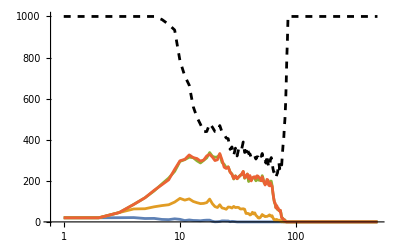

```mathematica
patch=1;
DataPatch = DataSimulation[[patch,All,All]];
DataGametes=Table[ConvertToGametes[DataPatch[[i,;;]],pars],{i,1,NGenerations}];
DataLoci=Table[GametesToAlleleFrequency[DataGametes[[i,;;]],pars],{i,1,NGenerations}];
DataFinal = Table[{DataLoci[[i]][[1]][[2]],DataLoci[[i]][[2]][[2]],DataLoci[[i]][[3]][[2]],DataLoci[[i]][[4]][[2]]},{i,1,NGenerations}];
plot1a=ListLinePlot[Transpose[DataFinal],PlotRange->{All,{0,MaxPopSize}},ScalingFunctions->{"Log","Linear"}];
plot1b=ListLinePlot[Transpose[Table[DataLoci[[i]][[1]][[1]]+DataLoci[[i]][[1]][[2]] ,{i,1,NGenerations}]],ScalingFunctions->{"Log","Linear"},PlotStyle->{Black,Dashed}];
Show[plot1a,plot1b]
```

Patch 1

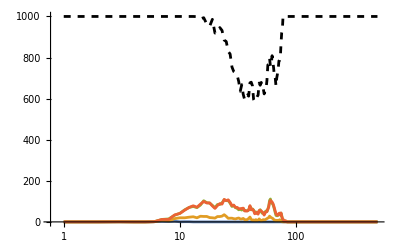

```mathematica
patch=2;
DataPatch = DataSimulation[[patch,All,All]];
DataGametes=Table[ConvertToGametes[DataPatch[[i,;;]],pars],{i,1,NGenerations}];
DataLoci=Table[GametesToAlleleFrequency[DataGametes[[i,;;]],pars],{i,1,NGenerations}];
DataFinal = Table[{DataLoci[[i]][[1]][[2]],DataLoci[[i]][[2]][[2]],DataLoci[[i]][[3]][[2]],DataLoci[[i]][[4]][[2]]},{i,1,NGenerations}];
plot1a=ListLinePlot[Transpose[DataFinal],PlotRange->{All,{0,MaxPopSize}},ScalingFunctions->{"Log","Linear"}];
plot1b=ListLinePlot[Transpose[Table[DataLoci[[i]][[1]][[1]]+DataLoci[[i]][[1]][[2]] ,{i,1,NGenerations}]],ScalingFunctions->{"Log","Linear"},PlotStyle->{Black,Dashed}];
Show[plot1a,plot1b]
```

Patch  2

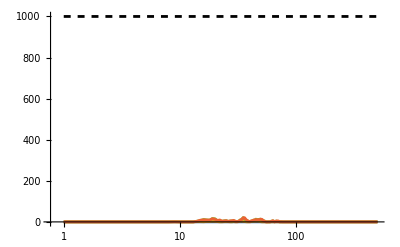

```mathematica
patch=3;
DataPatch = DataSimulation[[patch,All,All]];
DataGametes=Table[ConvertToGametes[DataPatch[[i,;;]],pars],{i,1,NGenerations}];
DataLoci=Table[GametesToAlleleFrequency[DataGametes[[i,;;]],pars],{i,1,NGenerations}];
DataFinal = Table[{DataLoci[[i]][[1]][[2]],DataLoci[[i]][[2]][[2]],DataLoci[[i]][[3]][[2]],DataLoci[[i]][[4]][[2]]},{i,1,NGenerations}];
plot1a=ListLinePlot[Transpose[DataFinal],PlotRange->{All,{0,MaxPopSize}},ScalingFunctions->{"Log","Linear"}];
plot1b=ListLinePlot[Transpose[Table[DataLoci[[i]][[1]][[1]]+DataLoci[[i]][[1]][[2]] ,{i,1,NGenerations}]],ScalingFunctions->{"Log","Linear"},PlotStyle->{Black,Dashed}];
Show[plot1a,plot1b]
```